```mathematica
Clear["Global`*"]
```

```mathematica
MM[d_,ps_,η_]:=d(1-ps)+η ps;
NN[d_,ps_]:=1/((1-d)(1-ps))-1;
AA[a_,b_,d_,ps_,η_]:=1+MM[d,ps,η] b^2+η NN[d,ps](a^2+MM[d,ps,η] b^2);
```

#### The success rate

```mathematica
SS[a_,b_,d_,ps_,η_]:=1/AA[a,b,d,ps,η];
```

#### The fidelity

```mathematica
FF[a_,b_,d_,ps_,η_]:=(1+(MM[d,ps,η]+η NN[d,ps])a^2 b^2+η MM[d,ps,η]NN[d,ps] b^4)/AA[a,b,d,ps,η];
```

```mathematica
F2[a_,b_,d_,ps_,η_]:=(1+(d(1-ps)+η ps+η/((1-d)(1-ps))-η) a^2 b^2+η(d(1-ps)+η ps)(1/((1-d)(1-ps))-1)b^4)/AA[a,b,d,ps,η];
```

```mathematica
Bond[d_,β_]:=1/2(d-1/(d*β^2)+√((d-1/(d*β^2))^2+4(1-d)));
```

```mathematica
Bond[0.5,1]
```

0.280776

```mathematica
Plot3D[Bond[d,β],
{d,0,1},{β,0,1},
PlotRange->Full,
AxesLabel->{"d","|β|","(η^-)_c"},
ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],BaseStyle->{FontFamily->"Times", FontSize->12}]
```

-Graphics3D-

```mathematica
?Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions.

```mathematica
FindMaximum[Bond[x,β],{x,0,1},{β,0,1}]
```

```mathematica
FindMaximum[{Bond[x,β],0<x<1,0<β<1},{x,0.5},{β,1}]
```

{0.295598,{x→0.647799,β→1.}}

```mathematica
Judg[0.5]
```

0.137459

```mathematica
Judg[0.3]
```

0.108112

```mathematica
a=1/(√2);
b=1/(√2);
```

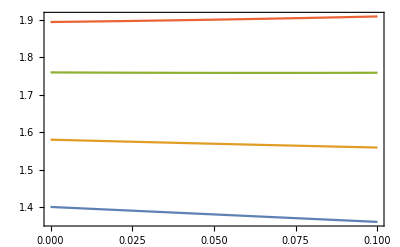

```mathematica
Plot[
{
AA[a,b,0.8,ps,0.0],
AA[a,b,0.8,ps,0.05],
AA[a,b,0.8,ps,0.1],
AA[a,b,0.8,ps,0.13745]
},
{ps,0,0.1},
Frame->True,
PlotRange->Full]
```

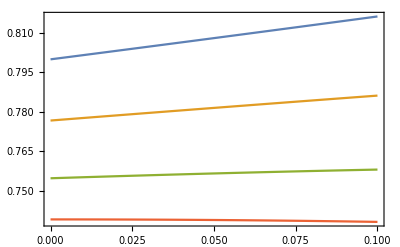

```mathematica
Plot[
{
SS[a,b,0.5,ps,0.0],
SS[a,b,0.5,ps,0.05],
SS[a,b,0.5,ps,0.1],
SS[a,b,0.5,ps,0.13745]
},
{ps,0,0.1},
Frame->True,
PlotRange->Full]
```

```mathematica
|
```

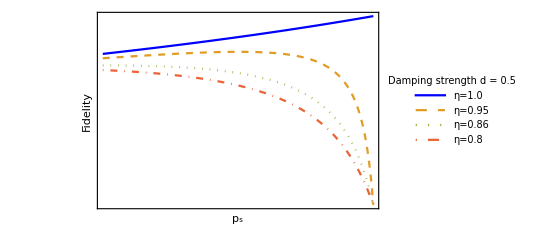

```mathematica
Plot[
{
FF[a,b,0.5,ps,0.0],
FF[a,b,0.5,ps,0.05],
FF[a,b,0.5,ps,0.13745],
FF[a,b,0.5,ps,0.2]
},
{ps,0,1},
Frame->True,PlotRange->Full,
FrameLabel->{"\!\(\*SubscriptBox[\(p\), \(s\)]\)","Fidelity"},RotateLabel->True,FrameStyle->Directive[Black],FrameTicks->{{None,All},{None,All}},PlotLegends->Placed[LineLegend[{"η=1.0","η=0.95","η=0.86","η=0.8"},
LegendLabel->"Damping strength d = 0.5",
LegendLayout->{"Row",2}],{Left,Bottom}],PlotStyle->{Blue,Dashed,Dotted,DotDashed},BaseStyle->{FontFamily->"Times",FontSize->12}]
```